## Read data

```mathematica
a=Import["~/t191229a.csv","CSV"];
```

```mathematica
Dimensions[a]
```

{9881,11}

```mathematica
b=Transpose[a];
```

```mathematica
Dimensions[b]
```

{11,9881}

```mathematica
time=b[[1]];
```

## x1 = Tc1, x2 = Tc2, x3 = Tc4, x4 = Tc5, x5 = Tc3 - 1, x6 =Tc 3 - 2, x7 = Tc3 - 3

```mathematica
x1=b[[2]];x2=b[[3]];
```

```mathematica
x3=b[[4]];x4=b[[5]];
```

```mathematica
x5=b[[6]];x6=b[[7]];x7=b[[8]];
```

## Time Convolution

## 620 - 810

```mathematica
time[[2]]
```

5.7

```mathematica
time[[8000]]
```

805.5

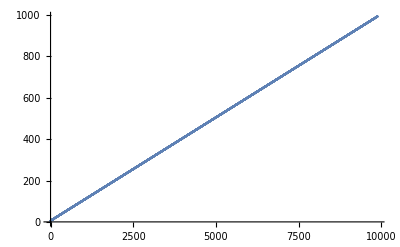

```mathematica
ListPlot[time]
```

```mathematica
y1={};y2={};
```

```mathematica
t1={};
```

```mathematica
x1[[1]]
```

19.1875

```mathematica
Do[If[time[[i1]]>619.9  && time[[i1]]<810.1,AppendTo[y1,x1[[i1]]]],{i1,Length[time]}]
```

```mathematica
Do[If[time[[i1]]>619.9  && time[[i1]]<810.1,AppendTo[y2,x2[[i1]]]],{i1,Length[time]}]
```

```mathematica
Do[If[time[[i1]]>619.9  && time[[i1]]<810.1,AppendTo[t1,time[[i1]]]],{i1,Length[time]}]
```

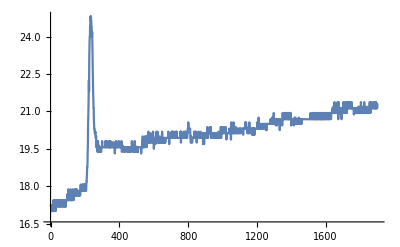

```mathematica
ListPlot[y1,Joined->True,PlotRange->All]
```

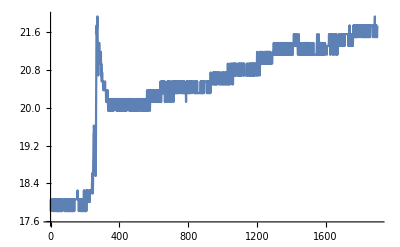

```mathematica
ListPlot[y2,Joined->True,PlotRange->All]
```

## Moving Average

```mathematica
v1=MovingAverage[y1,10];
```

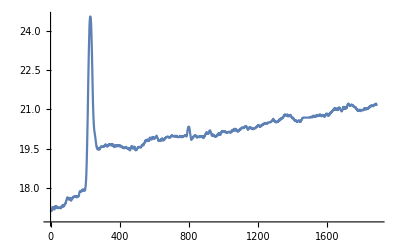

```mathematica
ListPlot[v1,Joined->True,PlotRange->All]
```

```mathematica
v2=MovingAverage[y2,10];
```

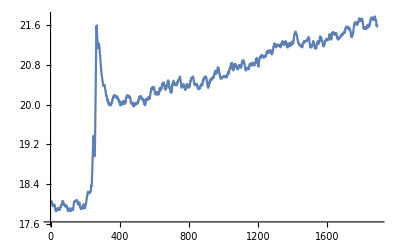

```mathematica
ListPlot[v2,Joined->True,PlotRange->All]
```

```mathematica
tt1=MovingAverage[t1,10];
```

```mathematica
Length[tt1]
```

1882

```mathematica
Length[v1]
```

1882

## time correlation

```mathematica
z=(0.1/201.)Table[v1.RotateLeft[v2,k],{k,1,Length[v1]}];
```

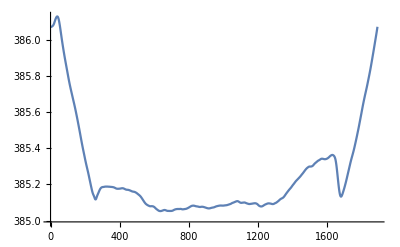

```mathematica
ListPlot[z,Joined->True,PlotRange->All]
```

```mathematica
vv1=Table[{tt1[[i]],v1[[i]]},{i,Length[tt1]}];
```

```mathematica
vv2=Table[{tt1[[i]],v2[[i]]},{i,Length[tt1]}];
```

## Delay Time

```mathematica
zm=Max[Table[z[[i]],{i,1,200}]]
```

386.128

```mathematica
x={}
```

{}

```mathematica
Do[If[z[[i]]==zm,AppendTo[x,i]],{i,Length[z]}]
```

```mathematica
x[[1]]
```

39

```mathematica
tl=tt1[[x[[1]]]]
```

624.25

```mathematica
ts=tt1[[1]]
```

620.45

## delay time

```mathematica
tl-ts
```

3.8